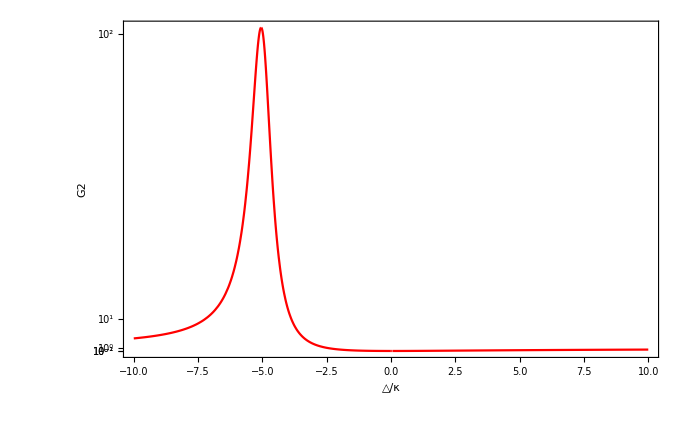

```mathematica
rule={Ω->0.1,κ->1,χ->5};
C0=1;
C1=-Ω/(△-(I*κ)/2);
C2=√2 Ω^2/((△-(I*κ)/2)*(2△-(I*κ)+2χ));
C1=C1//.rule//FullSimplify;
C2=C2//.rule//FullSimplify;
N1=Abs[C0*Conjugate[C0]]+Abs[C1*Conjugate[C1]]+Abs[C2*Conjugate[C2]];
P1=Abs[C1*Conjugate[C1]]/N1;
P2=Abs[C2*Conjugate[C2]]/N1;
G[△_]=(2*P2)/P1^2;
Plot[G[△],{△,-10,10},PlotRange->All,Frame->True,(*启用边框*)FrameLabel->{"△/κ","G2"},(*设置坐标轴标签*)FrameStyle->Directive[Black,Thick],(*设置边框样式*)FrameTicksStyle->Directive[FontFamily->"Arial",12],(*设置刻度标签样式*)FrameTicks->{Automatic,(*让Mathematica自动计算横轴刻度*){{0.01,"10^-2"},{0.1,"10^-1"},{1,"10^0"},{10,"10^1"},{100,"10^2"}} (*自定义纵轴刻度*)},PlotStyle->Red            (*设置数据线颜色*)]
```